```mathematica
$Assumptions = {x ∈ Reals, x>0 , n∈ Integers, n>0, a>0, s>0, u>0}
```

{x∈Reals,x>0,n∈Integers,n>0,a>0,s>0,u>0}

```mathematica
Hk[n_,x_] = ((ⅈ)^(-n-1) Exp[ⅈ x] / (  x )) Sum[ ((n+m)! / ( m! (n-m)! )) (-2 I x)^(-m),{m,0,n}]
```

(ⅈ^(-1-n) √(2/π) √(-ⅈ x) BesselK[1/2 (-1-2 n),-ⅈ x])/x

```mathematica
sbexpand = {SphericalBesselJ[n_,x_] ->FullSimplify[ComplexExpand[Re[Hk[n,x]]]],  SphericalBesselY[n_,x_] ->  FullSimplify[ComplexExpand[Im[Hk[n,x]]]] }
```

{SphericalBesselJ[n_,x_]→1/(√x)√(2/π) (Cos[1/4 (3+2 n) π] Re[BesselK[1/2+n,-ⅈ x]]+Im[BesselK[1/2+n,-ⅈ x]] Sin[1/4 (3+2 n) π]),SphericalBesselY[n_,x_]→1/(√x)√(2/π) (Cos[1/4 (3+2 n) π] Im[BesselK[1/2+n,-ⅈ x]]-Re[BesselK[1/2+n,-ⅈ x]] Sin[1/4 (3+2 n) π])}

```mathematica
Clear[G,P,Q]
```

```mathematica
expandgpq = {G[n_,m_] -> (n+m)! / ( m! (n-m)!),
P[n_,x_] -> Sum[(-1)^m  G[n, 2m] (2 x)^(-2m), {m,0,n/2}],
Q[n_,x_] -> Sum[ (-1)^m G[n,2m+1] (2 x)^(-2m-1),{m,0,(n-1)/2}]}
```

{G[n_,m_]→((m+n)!)/(m! (-m+n)!),P[n_,x_]→∑_(m=0)^(n/2) (-1)^m 2^(-2 m) x^(-2 m) G[n,2 m],Q[n_,x_]→∑_(m=0)^(1/2 (-1+n)) (-1)^m 2^(-1-2 m) x^(-1-2 m) G[n,1+2 m]}

```mathematica
sbexpand2 = {SphericalBesselJ[n_,x_] -> (1/x) ( P[n,x] Sin[x-Pi n/2] + Q[n,x] Cos[x-Pi n/2]),
SphericalBesselY[n_,x_] ->(-1)^(n+1) (1/x) (P[n,x] Cos[ x+ Pi n /2] - Q[n,x] Sin[x + Pi n/2])}
```

{SphericalBesselJ[n_,x_]→(Cos[(n π)/2-x] Q[n,x]-P[n,x] Sin[(n π)/2-x])/x,SphericalBesselY[n_,x_]→((-1)^(1+n) (Cos[(n π)/2+x] P[n,x]-Q[n,x] Sin[(n π)/2+x]))/x}

```mathematica
({SphericalBesselJ[n,x], SphericalBesselY[n,x]}/. sbexpand ) == ({ SphericalBesselJ[n,x], SphericalBesselY[n,x]} /. sbexpand2 //. expandgpq) /. n->3 // FullSimplify
```

{1/x^4(-x (-15+x^2) Cos[x]+Re[ⅇ^(ⅈ x) (-15 ⅈ+x (-15+x (6 ⅈ+x)))]+3 (-5+2 x^2) Sin[x]),1/x^4(3 (5-2 x^2) Cos[x]+Im[ⅇ^(ⅈ x) (-15 ⅈ+x (-15+x (6 ⅈ+x)))]-x (-15+x^2) Sin[x])}=={0,0}

```mathematica
transcossin:={a_ Cos[z_]+b_ Sin[z_]->Sqrt[1+b^2/a^2] a Cos[z-ArcTan[b/a]]}
getcosarg := { a_ Cos[z_]  ->  z}
```

```mathematica
falpha=Simplify[-(((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r u]+BesselJ[1/2+n,r u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u]))/.{r->a}]
```

-((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u]-BesselJ[1/2+n,a u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])

```mathematica
transsbessel={BesselJ[n_+2 nn_(1/2),z_]->SphericalBesselJ[n+nn-1/2,z] / Sqrt[Pi/(2 z)],BesselY[n_+2 nn_ (1/2),z_]->SphericalBesselY[n+nn-1/2,z] / Sqrt[Pi / (2z)]}
```

{BesselJ[n_+nn_,z_]→(√(2/π) SphericalBesselJ[-1/2+n+nn,z])/(√(1/z)),BesselY[n_+nn_,z_]→(√(2/π) SphericalBesselY[-1/2+n+nn,z])/(√(1/z))}

```mathematica
transsbessel={BesselJ[n_+2 nn_(1/2),z_]->SphericalBesselJ[n+nn-1/2,z] / Sqrt[Pi/(2 z)],BesselY[n_+2 nn_ (1/2),z_]->SphericalBesselY[n+nn-1/2,z] / Sqrt[Pi / (2z)]}
```

{BesselJ[n_+nn_,z_]→(√(2/π) SphericalBesselJ[-1/2+n+nn,z])/(√(1/z)),BesselY[n_+nn_,z_]→(√(2/π) SphericalBesselY[-1/2+n+nn,z])/(√(1/z))}

```mathematica
falphahb = falpha /. transsbessel // Simplify
```

1/π 2 √(a s) u ((-n+h s) SphericalBesselJ[n,s u] SphericalBesselY[n,a u]+s u SphericalBesselJ[1+n,s u] SphericalBesselY[n,a u]+SphericalBesselJ[n,a u] ((n-h s) SphericalBesselY[n,s u]-s u SphericalBesselY[1+n,s u]))

```mathematica
1/π(2 √(a s) u ((-n+h s) SphericalBesselJ[n,s u] SphericalBesselY[n,a u]+s u SphericalBesselJ[1+n,s u] SphericalBesselY[n,a u]+SphericalBesselJ[n,a u] ((n-h s) SphericalBesselY[n,s u]-s u SphericalBesselY[1+n,s u])))
```

1/π 2 √(a s) u ((-n+h s) SphericalBesselJ[n,s u] SphericalBesselY[n,a u]+s u SphericalBesselJ[1+n,s u] SphericalBesselY[n,a u]+SphericalBesselJ[n,a u] ((n-h s) SphericalBesselY[n,s u]-s u SphericalBesselY[1+n,s u]))

```mathematica
tmp =falphahb /. sbexpand2
```

1/π 2 √(a s) u (1/(a s u^2)(-1)^(1+n) (-n+h s) (Cos[(n π)/2+a u] P[n,a u]-Q[n,a u] Sin[(n π)/2+a u]) (Cos[(n π)/2-s u] Q[n,s u]-P[n,s u] Sin[(n π)/2-s u])+1/(a u)(-1)^(1+n) (Cos[(n π)/2+a u] P[n,a u]-Q[n,a u] Sin[(n π)/2+a u]) (Cos[1/2 (1+n) π-s u] Q[1+n,s u]-P[1+n,s u] Sin[1/2 (1+n) π-s u])+1/(a u)(Cos[(n π)/2-a u] Q[n,a u]-P[n,a u] Sin[(n π)/2-a u]) (1/(s u)(-1)^(1+n) (n-h s) (Cos[(n π)/2+s u] P[n,s u]-Q[n,s u] Sin[(n π)/2+s u])-(-1)^(2+n) (Cos[1/2 (1+n) π+s u] P[1+n,s u]-Q[1+n,s u] Sin[1/2 (1+n) π+s u])))

```mathematica
tmp2 =tmp  // TrigFactor// Simplify // TrigFactor
```

1/(π √(a s) u)2 (Cos[(a-s) u] (s u P[n,a u] P[1+n,s u]-n P[n,s u] Q[n,a u]+h s P[n,s u] Q[n,a u]+n P[n,a u] Q[n,s u]-h s P[n,a u] Q[n,s u]+s u Q[n,a u] Q[1+n,s u])+(-n P[n,a u] P[n,s u]+h s P[n,a u] P[n,s u]-s u P[1+n,s u] Q[n,a u]-n Q[n,a u] Q[n,s u]+h s Q[n,a u] Q[n,s u]+s u P[n,a u] Q[1+n,s u]) Sin[(a-s) u])

```mathematica
transcossingroup := { a_ Cos[x_] + b_ Cos[x_] -> (a + b) Cos[x], a_ Sin[x_] + b_ Sin[x_] -> (a+b) Sin[x]}
```

```mathematica
falpha2 = tmp2//. transcossingroup  /. transcossin // FullSimplify
```

1/(π √(a s) u)2 Cos[(a-s) u-ArcTan[(-Q[n,a u] (s u P[1+n,s u]+(n-h s) Q[n,s u])+P[n,a u] ((-n+h s) P[n,s u]+s u Q[1+n,s u]))/(P[n,a u] (s u P[1+n,s u]+(n-h s) Q[n,s u])+Q[n,a u] ((-n+h s) P[n,s u]+s u Q[1+n,s u]))]] (P[n,a u] (s u P[1+n,s u]+(n-h s) Q[n,s u])+Q[n,a u] ((-n+h s) P[n,s u]+s u Q[1+n,s u])) √(1+(Q[n,a u] (s u P[1+n,s u]+(n-h s) Q[n,s u])+P[n,a u] ((n-h s) P[n,s u]-s u Q[1+n,s u]))^2/(P[n,a u] (s u P[1+n,s u]+(n-h s) Q[n,s u])+Q[n,a u] ((-n+h s) P[n,s u]+s u Q[1+n,s u]))^2)

```mathematica
falphaaux = falpha2  /. getcosarg // FullSimplify
```

(a-s) u-ArcTan[(-Q[n,a u] (s u P[1+n,s u]+(n-h s) Q[n,s u])+P[n,a u] ((-n+h s) P[n,s u]+s u Q[1+n,s u]))/(P[n,a u] (s u P[1+n,s u]+(n-h s) Q[n,s u])+Q[n,a u] ((-n+h s) P[n,s u]+s u Q[1+n,s u]))]

```mathematica
falpharem = 1/(π √(a s) u)2(P[n,a u] (s u P[1+n,s u]+(n-h s) Q[n,s u])+Q[n,a u] ((-n+h s) P[n,s u]+s u Q[1+n,s u])) √(1+(Q[n,a u] (s u P[1+n,s u]+(n-h s) Q[n,s u])+P[n,a u] ((n-h s) P[n,s u]-s u Q[1+n,s u]))^2/(P[n,a u] (s u P[1+n,s u]+(n-h s) Q[n,s u])+Q[n,a u] ((-n+h s) P[n,s u]+s u Q[1+n,s u]))^2)
```

1/(π √(a s) u)2 (P[n,a u] (s u P[1+n,s u]+(n-h s) Q[n,s u])+Q[n,a u] ((-n+h s) P[n,s u]+s u Q[1+n,s u])) √(1+(Q[n,a u] (s u P[1+n,s u]+(n-h s) Q[n,s u])+P[n,a u] ((n-h s) P[n,s u]-s u Q[1+n,s u]))^2/(P[n,a u] (s u P[1+n,s u]+(n-h s) Q[n,s u])+Q[n,a u] ((-n+h s) P[n,s u]+s u Q[1+n,s u]))^2)

```mathematica
falphaaux //. { (s u P[1+n,s u]+(n-h s) Q[n,s u])-> S, ((-n+h s) P[n,s u]+s u Q[1+n,s u]) -> T} // FullSimplify
```

(a-s) u-ArcTan[(T P[n,a u]-S Q[n,a u])/(S P[n,a u]+T Q[n,a u])]

```mathematica
falpha2 //. { (s u P[1+n,s u]+(n-h s) Q[n,s u])-> S, ((-n+h s) P[n,s u]+s u Q[1+n,s u]) -> T} // FullSimplify
```

1/(π √(a s) u)2 Cos[(a-s) u-ArcTan[(T P[n,a u]-S Q[n,a u])/(S P[n,a u]+T Q[n,a u])]] (S P[n,a u]+T Q[n,a u]) √(1+(S Q[n,a u]+P[n,a u] ((n-h s) P[n,s u]-s u Q[1+n,s u]))^2/(S P[n,a u]+T Q[n,a u])^2)

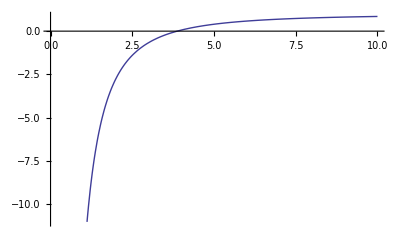

```mathematica
Plot[P[3,x] //. expandgpq,{x,0,10}]
```

```mathematica
Plot[falpha2 //. expandgpq /. {a->10^-7, s ->10^-8,h->10^18, n->4},{u,0,1000000000}]
```

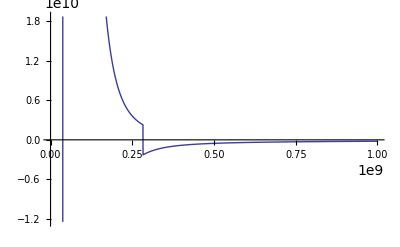

```mathematica
Plot[falpharem//. expandgpq /. {a->10^-7, s ->10^-8,h->10^18, n->4},{u,0,1000000000}]
```

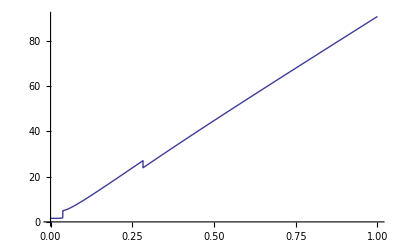

```mathematica
Plot[falphaaux //. expandgpq /. {a->10^-7, s ->10^-8,h->10^18, n->4},{u,0,1000000000}]
```